# Data Set 2

```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;

set=2;
```

## Data Import

$SPEC_ID:
No sample description was entered.
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/23/2015 08:25:16
$MEAS_TIM:
3600 3737
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

\begin{array}{c}
 \text{$\$$SPEC$\_$ID:} \\
 \text{No sample description was entered.} \\
 \text{$\$$SPEC$\_$REM:} \\
 \text{DET$\#$ 1} \\
 \text{DETDESC$\#$ HPGe Detector 1} \\
 \text{AP$\#$ GammaVision Version 6.07} \\
 \text{$\$$DATE$\_$MEA:} \\
 \text{10/23/2015 08:25:16} \\
 \text{$\$$MEAS$\_$TIM:} \\
 \text{3600 3737} \\
 \text{$\$$DATA:} \\
 \text{0 8191} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{$\$$ROI:} \\
 0 \\
 \text{$\$$PRESETS:} \\
 \text{Live Time} \\
 3600 \\
 0 \\
 \text{$\$$ENER$\_$FIT:} \\
 \text{0.137869 0.366631} \\
 \text{$\$$MCA$\_$CAL:} \\
 3 \\
 \text{1.378689E-001 3.666307E-001 -4.415950E-008 keV} \\
 \text{$\$$SHAPE$\_$CAL:} \\
 3 \\
 \text{2.301834E+000 9.195991E-004 -5.357180E-008} \\
\end{array}

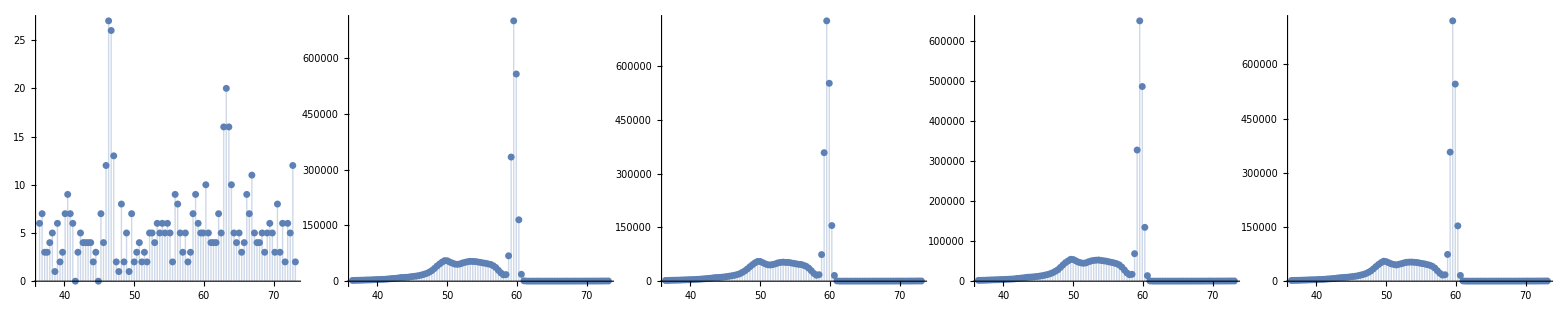

```mathematica
filenames={
"Background-10232015.Spe",
"Am-241-1hr-10232015.Spe",
"Am-241-1hrTrial2-10232015.Spe",
"Am-241-ThickFilm-1hr-10232015.Spe",
"Am-241-ThinFilm-1hr-10232015.Spe"};

m=Length[filenames]-1;
For[n=1,n≤m+1,n++,
imported=Import[filenames[[n]],"Data"];
times=ToExpression[StringSplit[imported[[10]]]];
If[n==2,
Print[TableForm[imported[[;;15]]]];
Print[TableForm[imported[[-16;;]]]];
Print[TeXForm[TableForm[Drop[imported,{16,Length[imported]-16}]]]];
];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
energy[n-1]=ToExpression[StringSplit[imported[[-7]]]];
data[n-1]=Table[{i,energy[n-1][[1]]+energy[n-1][[2]](i-1),freq[[i]]},{i,Length[freq]}];
]
Grid[{Table[ListPlot[data[i][[100;;200,{2,3}]],ImageSize->Medium,PlotRange->All,Filling->Bottom],{i,0,m}]}]
Clear[n,filenames,imported,times,deadtime,freq]
```

## Data Analysis

## Equations

```mathematica
F[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
G[x_,mu_,sigma_,a_]:=Sum[F[x,mu[[i]],sigma[[i]],a[[i]]],{i,1,Length[mu]}]
fwhm[sigma_]:=2*sigma*Sqrt[2*Log[2]];

err[F_,w__]:={F[Map[First,List[w]]/.List->Sequence],Block[{parms=Table[Unique[],{x,1,Length[List[w]]}],values=Table[List[w][[i,1]],{i,1,Length[List[w]]}],errors=Table[List[w][[i,2]],{i,1,Length[List[w]]}]},Sqrt[Total[Table[(D[F[parms/.List->Sequence],parms[[i]]]*errors[[i]])^2,{i,1,Length[values]}]/.Table[parms[[i]]->values[[i]],{i,1,Length[values]}]]]]}
```

## Cubic Fit

| Estimate | Standard Error | t-Statistic | P-Value
a | 518.571 | 261.188 | 1.98543 | 0.0874787
b | -88994.2 | 45807.2 | -1.9428 | 0.09315
c | 5.0753×10^6 | 2.67664×10^6 | 1.89614 | 0.0997705
d | -9.61509×10^7 | 5.21111×10^7 | -1.84511 | 0.107535
mu | 59.6306 | 0.000746334 | 79898. | 1.27064×10^-32
sigma | 0.37086 | 0.00116796 | 317.528 | 8.11344×10^-16
p | 723225. | 1977.47 | 365.733 | 3.01688×10^-16

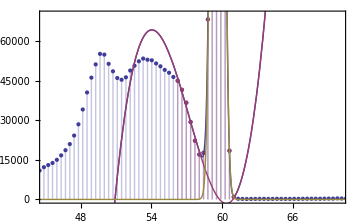

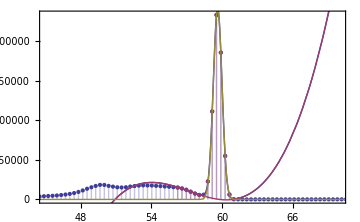

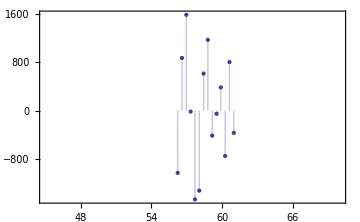

```mathematica
region={154,167};
Clear[a,b,c,d,mu,sigma,p]
viewingregion={50,200};viewingrange={45,70};imagesize=Medium;fontsize=12;theme="Classic";

guess={{a,361},{b,-61524},{c,3473469},{d,-65035121},{mu,59.6},{sigma,0.37},{p,670000}};

k=1;
cubic[k]=NonlinearModelFit[data[k][[region[[1]];;region[[2]],{2,3}]],a x^3+b x^2+c x+d+F[x,mu,sigma,p],guess,x];

cubic[k]["ParameterTable"]
cubicparams[k]=cubic[k]["BestFitParameters"][[All,2]];

Show[ListPlot[{data[k][[viewingregion[[1]];;viewingregion[[2]],{2,3}]],data[k][[region[[1]];;region[[2]],{2,3}]]},Filling->Axis,PlotRange->All,PlotTheme->theme],Plot[{cubic[k]["BestFit"],cubicparams[k][[1]]x^3+cubicparams[k][[2]]x^2+cubicparams[k][[3]]x+cubicparams[k][[4]],F[x,cubicparams[k][[-3]],cubicparams[k][[-2]],cubicparams[k][[-1]]]},{x,-10,100},PlotTheme->theme],PlotRange->{viewingrange,{0,70000}},Frame->{{True,False},{True,False}},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]

Show[ListPlot[{data[k][[viewingregion[[1]];;viewingregion[[2]],{2,3}]],data[k][[region[[1]];;region[[2]],{2,3}]]},Filling->Axis,PlotRange->All,PlotTheme->theme],Plot[{cubic[k]["BestFit"],cubicparams[k][[1]]x^3+cubicparams[k][[2]]x^2+cubicparams[k][[3]]x+cubicparams[k][[4]],F[x,cubicparams[k][[-3]],cubicparams[k][[-2]],cubicparams[k][[-1]]]},{x,-10,100},PlotTheme->theme],PlotRange->{viewingrange,{0,700000}},Frame->{{True,False},{True,False}},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]

ListPlot[Join[Table[{energy[k][[1]]+energy[k][[2]](i-1)},{i,region[[1]],region[[2]]}],Transpose[{cubic[k]["FitResiduals"]}],2],Filling->Axis,Frame->{{True,False},{True,False}},FrameTicks->{{True,False},{True,False}},Axes->True,PlotRange->{viewingrange,All},PlotTheme->theme,ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]
```

## Gaussian Fits

```mathematica
mu={24.2,48.4,49.7,53.2,56.0,59.6};
sigma={0.4,5.4,1.4,1.3,1.5,0.4};
a={6000,15000,30000,30000,30000,730000};
n=Length[mu];region={1,2000};
symbol={"μ","σ","a","I"};

For[k=1,k≤m,k++,
model[k]=NonlinearModelFit[data[k][[region[[1]];;region[[2]],{2,3}]],G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];

params[k]=model[k]["BestFitParameters"][[All,2]];
paramerrors[k]=model[k]["ParameterErrors"];

modeldata=Table[err[F,{i,0},{params[k][[n]],paramerrors[k][[n]]},{params[k][[2n]],paramerrors[k][[2n]]},{params[k][[3n]],paramerrors[k][[3n]]}],{i,Table[data[k][[i[[1]],2]],{i,Position[data[k][[;;200,2]],_?(params[k][[n]]-2*fwhm[params[k][[2n]]]<#<params[k][[n]]+2*fwhm[params[k][[2n]]]&)]}]}];
intensity[k]={Total[modeldata[[All,1]]*energy[k][[2]]],Sqrt[Total[(modeldata[[All,2]]*energy[k][[2]])^2]]};
Print[TableForm[Insert[Insert[

Table[{symbol[[i/n]],params[k][[i]],paramerrors[k][[i]],100*paramerrors[k][[i]]/params[k][[i]]},{i,{n,2n,3n}}],

Join[{symbol[[4]]},intensity[k],{100*intensity[k][[2]]/intensity[k][[1]]}],4]
,{{},{"Value"},{"Error"},{"Percent Error"}},1]]];
]
```

| Value | Error | Percent Error
μ | 59.6296 | 0.000217202 | 0.000364252
σ | 0.369496 | 0.000242754 | 0.0656987
a | 720759. | 377.348 | 0.0523543
I | 667558. | 309.985 | 0.0464356

| Value | Error | Percent Error
μ | 59.6136 | 0.000212177 | 0.000355921
σ | 0.367913 | 0.000236168 | 0.0641912
a | 740035. | 379.622 | 0.0512978
I | 682473. | 311.045 | 0.0455762

| Value | Error | Percent Error
μ | 59.607 | 0.000226443 | 0.000379893
σ | 0.368336 | 0.000251178 | 0.0681927
a | 661862. | 361.249 | 0.0545807
I | 611082. | 296.146 | 0.0484626

| Value | Error | Percent Error
μ | 59.6122 | 0.000212635 | 0.000356697
σ | 0.368085 | 0.00023694 | 0.064371
a | 733900. | 377.319 | 0.0514128
I | 677131. | 309.276 | 0.0456745

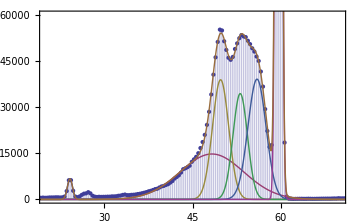
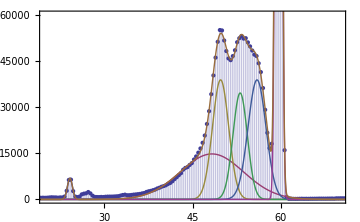
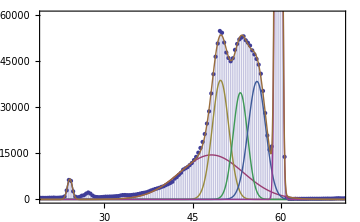
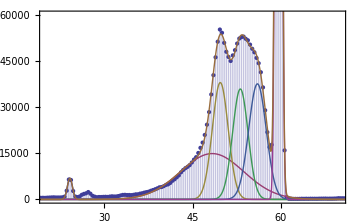
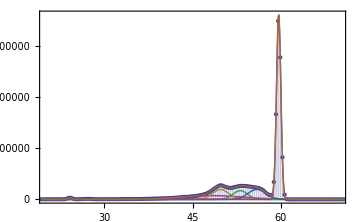
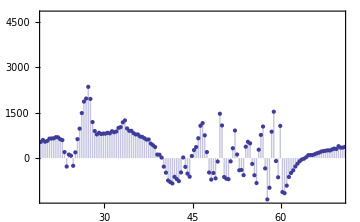
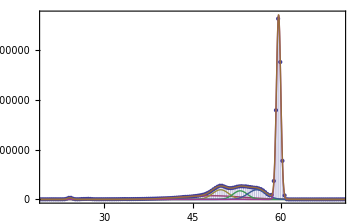
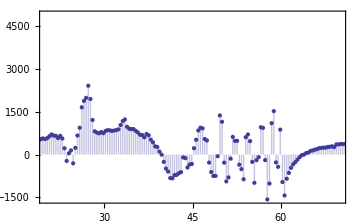
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- -Graphics- | -Graphics- -Graphics- | -Graphics- -Graphics- | -Graphics- -Graphics-

```mathematica
viewingrange={20,70};
theme="Classic";imagesize=Medium;fontsize=12;

Grid[Transpose[Table[{Show[ListPlot[data[k][[region[[1]];;region[[2]],{2,3}]],Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[k][[i]],params[k][[i+n]],params[k][[i+2n]]],{i,1,n}],{G[x,params[k][[;;n]],params[k][[n+1;;2n]],params[k][[2n+1;;3n]]]}],{x,-10,200},PlotRange->All,PlotTheme->theme],Frame->{{True,False},{True,False}},PlotRange->{viewingrange,{0,60000}},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}],

Show[ListPlot[data[k][[region[[1]];;region[[2]],{2,3}]],Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[k][[i]],params[k][[i+n]],params[k][[i+2n]]],{i,1,n}],{G[x,params[k][[;;n]],params[k][[n+1;;2n]],params[k][[2n+1;;3n]]]}],{x,-10,200},PlotRange->All,PlotTheme->theme],Frame->{{True,False},{True,False}},PlotRange->{viewingrange,All},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]

ListPlot[Join[Table[{energy[k][[1]]+energy[k][[2]](i-1)},{i,region[[1]],region[[2]]}],Transpose[{model[k]["FitResiduals"]}],2],Filling->Axis,Frame->{{True,False},{True,False}},FrameTicks->{{True,False},{True,False}},Axes->True,PlotRange->{viewingrange,All},PlotTheme->theme,ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]},{k,1,4}]]]
```

```mathematica
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;
runs={"Source 1","Source 2","Thick","Thin"};
thickness={40,0.01};

Print[TableForm[Insert[Table[Join[{runs[[i]]},intensity[i],{100*intensity[i][[2]]/intensity[i][[1]]}],{i,1,m}],{{},{"Intensity"},{"Error"},"Percent Error"},1]]]

Print["\nTrial 1"]
atten=err[coeff,intensity[1],intensity[3],thickness];
Print["attenuation coefficient = ",Join[atten,{100*atten[[2]]/atten[[1]]}]]
thin=err[coeff,intensity[1],intensity[4],atten];Print["thin foil measurement = ",Join[thin,{100*thin[[2]]/thin[[1]]}]]

Print["\nTrial 2"]
atten=err[coeff,intensity[2],intensity[3],thickness];
Print["attenuation coefficient = ",Join[atten,{100*atten[[2]]/atten[[1]]}]]
thin=err[coeff,intensity[2],intensity[4],atten];Print["thin foil measurement = ",Join[thin,{100*thin[[2]]/thin[[1]]}]]
```

| Intensity | Error | Percent Error
Source 1 | 667558. | 309.985 | 0.0464356
Source 2 | 682473. | 311.045 | 0.0455762
Thick | 611082. | 296.146 | 0.0484626
Thin | 677131. | 309.276 | 0.0456745

Trial 1

attenuation coefficient = {0.00220991,0.0000167887,0.759702}

thin foil measurement = {-6.44261,0.298772,-4.63743}

Trial 2

attenuation coefficient = {0.0027623,0.000016646,0.602615}

thin foil measurement = {2.84475,0.234216,8.23327}